# ŽAN POJE - 23211321

## 1.) Računanje vrednosti števila π

```mathematica
Get[NotebookDirectory[]<>"monteCarloPi.m"]
```

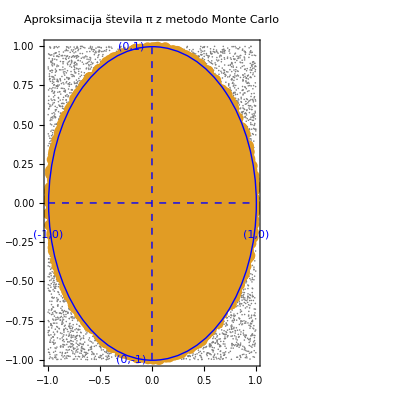

π_aproksimiran=3.144

```mathematica
MonteCarloPi[10000]
```

## 2.) Razvoj v vrsto in funkcija Manipulate

```mathematica
fun1[t_]=Sin[t]*t^2*Exp[-t];

fun2=Normal[Table[Series[fun1[t],{t,2,n}],{n,0,15}]];

Manipulate[Plot[{fun1[t],fun2[[r]]},{t,0,4},
AxesLabel->{"t","y"},
PlotLegends->{"sin(t) t^2 e^-t",StringForm["Taylorjeva vrsta reda ``.",r-1]}],
{r,1,11,1}]
```